## 13 TeV Plot m_H - tanβ

### Frame

System`ListPlotsDump`messageshead$2263::prng: Value of option PlotRange -> {{xmin,xmax},{ymin,ymax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

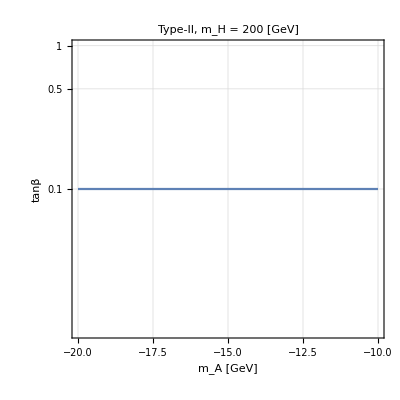

```mathematica
(*Create a nice looking Frame*)
SetOptions[ListPlot,BaseStyle->{FontSize->15}];
ticksyaxis = { 
 {Log10[0.1],"0.1"(*Superscript[10,-1]*)},{Log10[0.2],""},{Log10[0.3],""},{Log10[0.4],""},
{Log10[0.5],"0.5"},{Log10[0.6],""},{Log10[0.7],""},{Log10[0.8],""},{Log10[0.9],""},
 {Log10[1],1},{Log10[2],""},{Log10[3],""},{Log10[4],""},
{Log10[5],"5"},{Log10[6],""},{Log10[7],""},{Log10[8],""},{Log10[9],""},
 {Log10[10],10},{Log10[20],""},{Log10[30],""},{Log10[40],""},
{Log10[50],"50"},{Log10[60],""},{Log10[70],""},{Log10[80],""},{Log10[90],""},
 {Log10[100],100}};
MyFramecos=ListPlot[{{-10,-1},{-20,-1}},
PlotRange->{{xmin,xmax},{ymin,ymax}},
Frame->True, Axes->False,AspectRatio->1,FrameStyle->Directive[Black,Thick],
Joined->True,Filling->None,
GridLines->Automatic,
FrameTicks->{{ticksyaxis,None},{Automatic,None}},
FrameLabel->{Style["m_A [GeV]",Black,21],Style["tanβ",Black,21]},
PlotLabel->Style["Type-II, m_H = 200 [GeV]",Black,18],
Epilog->{
Inset[Style["cos(β-α) = 0",Red,15],{600,Log10[25]}],
Inset[Style["cos(β-α) = 0.2",Darker[Green],15],{600,Log10[10]}],
Inset[Style["cos(β-α) = 0.1",Blue,15],{600,Log10[15.7]}]

},
ImageSize->400]
```

### color set

RGBColor[1, 0, 0]

RGBColor[Rational[253, 255], Rational[103, 255], Rational[103, 255]]

RGBColor[Rational[48, 85], Rational[14, 15], Rational[48, 85]]

RGBColor[Rational[9, 17], Rational[206, 255], Rational[50, 51]]

RGBColor[1, Rational[28, 51], 0]

RGBColor[1, Rational[44, 51], Rational[2, 3]]

RGBColor[Rational[16, 17], Rational[44, 51], Rational[2, 51]]

RGBColor[Rational[49, 51], Rational[49, 51], Rational[10, 17]]

RGBColor[0, 1, 1]

RGBColor[Rational[203, 255], Rational[253, 255], Rational[253, 255]]

RGBColor[0.5, 0, 0.5]

RGBColor[Rational[13, 15], Rational[32, 51], Rational[13, 15]]

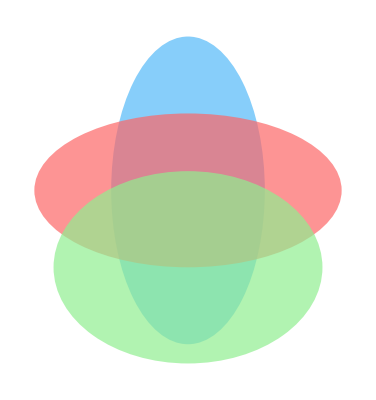

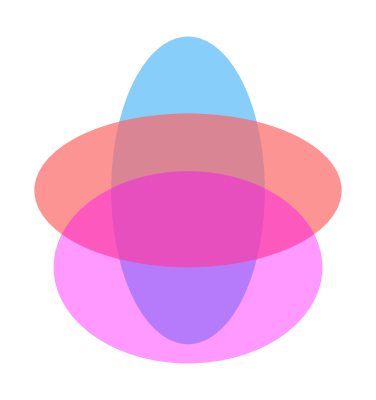

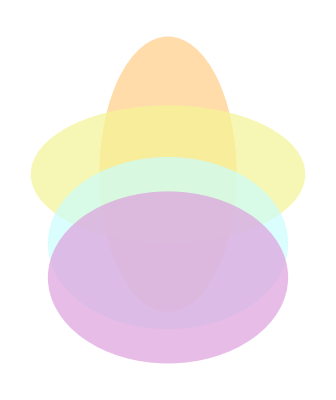

```mathematica
Red
clightred(*fd6767*)=RGBColor[253/255,103/255,103/255]
clightgreen=RGBColor[144/255,238/255,144/255]
clightskyblue=RGBColor[135/255,206/255,250/255]
orange=RGBColor[255/255,140/255,0/255]
clightorange=RGBColor[255/255,220/255,170/255]
yellow=RGBColor[240/255,220/255,10/255]

clightyellow=RGBColor[245/255,245/255,150/255]
Cyan
clightcyan=RGBColor[203/255,253/255,253/255]
Purple
clightpurple=RGBColor[221/255,160/255,221/255]


Graphics[{Directive[clightskyblue,Opacity[1] ],Disk[{0,0},{2,4}],Directive[clightred,Opacity[0.7] ],Disk[{0,0},{4,2}],Directive[clightgreen,Opacity[0.7] ],Disk[{0,-2},{3.5,2.5}]}]
Graphics[{Directive[clightskyblue,Opacity[1] ],Disk[{0,0},{2,4}],Directive[clightred,Opacity[0.7] ],Disk[{0,0},{4,2}],Directive[Magenta,Opacity[0.4] ],Disk[{0,-2},{3.5,2.5}]}]
Graphics[{Directive[clightorange,Opacity[1] ],Disk[{0,0},{2,4}],Directive[clightyellow,Opacity[0.7] ],Disk[{0,0},{4,2}],Directive[clightcyan,Opacity[0.7] ],Disk[{0,-2},{3.5,2.5}],Directive[clightpurple,Opacity[0.7] ],Disk[{0,-3},{3.5,2.5}]}]
```

double lim[exp_len]={lim_ggAzhbb,lim_bbAzhbb,lim_ppHZZ,lim_ppHhh,lim_ggHWW,lim_VBFHWW, \6
        lim_bbHbb,lim_bbHmumu,lim_ggHmumu,lim_bbHtautau,lim_ggHtautau,\5
        lim_bbAbb,lim_bbAmumu,lim_ggAmumu,lim_bbAtautau,lim_ggAtautau,\5
        lim_ggAZHbb,lim_bbAZHbb,lim_Htt,lim_Att,lim_ppAyy8,lim_ppHyy8,\6
        lim_Ayy13,lim_Hyy13,lim_bbA2tau,lim_haa2b2mu,lim_haa2b2tau,lim_haa4tau};6

### Type-I, m_A=m_H, cos(β-α)=0.1,Brhaa

```mathematica
clightred(*fd6767*)=RGBColor[253/255,103/255,103/255]
clightgreen=RGBColor[144/255,238/255,144/255]
clightskyblue=RGBColor[135/255,206/255,250/255]
PathDir=NotebookDirectory[];

(*DEFINE SETUP*)
xmin=10;xmax=1000;ymin=Log10[0.1];ymax=Log10[50];

(*Import Stuff

infile1>>mh>>mH>>mA>>cosba>>tb;5
infile1>>ggA8>>bbA8;2
infile1>>ggA13>>bbA13>>zA13>>wbfA13;4
infile1>>ggH13>>bbH13>>zH13>>wbfH13;4
infile1>>brAtautau>>brAmumu>>brAbb>>brAtt;4
infile1>>brAgg>>brAgaga>>brAzh>>brHtautau;4
infile1>>brHmumu>>brHbb>>brHtt>>brHZZ;4
infile1>>brHWW>>brHhh>>brHgg>>brHgaga;4
infile1>>brhbb>>brHAZ>>brAHZ;3
infile1>>gammatotH>>gammatotA;2
infile1>>ggh13>>bbh13>>WBFh13;3
infile1>>Zh13>>brhaa>>brhHH;3
infile1>>ggA8>>bbA8>>WBFA8>>ZA8;4
infile1>>ggH8>>bbH8>>WBFH8>>ZH8>>gammatoth;5
*)
results=Import[PathDir<>"mh2tb_20.05_noexo.txt","table"];
leng=Length[results];
mH=Table[results[[j,3]],{j,1,leng}];
tb=Table[Log10[results[[j,5]]],{j,1,leng}];
haa=Table[Max[results[[j,41]]],{j,1,leng}];

datahaa=Table[{mH[[j]],tb[[j]],haa[[j]]},{j,1,leng} ];


funchaa=Interpolation[datahaa,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightcyan,Opacity[0.5] ];lcolA=Cyan;
figbrhaa=RegionPlot[funchaa[x,y]>0.3,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLabel->"br_inv<0.3"]
```

RGBColor[Rational[253, 255], Rational[103, 255], Rational[103, 255]]

RGBColor[Rational[48, 85], Rational[14, 15], Rational[48, 85]]

RGBColor[Rational[9, 17], Rational[206, 255], Rational[50, 51]]

-Graphics-

### Type-I, m_A=m_H, cos(β-α)=0.1, AhZ

RGBColor[Rational[253, 255], Rational[103, 255], Rational[103, 255]]

RGBColor[Rational[48, 85], Rational[14, 15], Rational[48, 85]]

RGBColor[Rational[9, 17], Rational[206, 255], Rational[50, 51]]

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

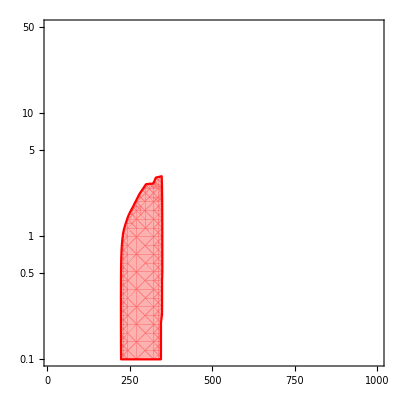

```mathematica
clightred(*fd6767*)=RGBColor[253/255,103/255,103/255]
clightgreen=RGBColor[144/255,238/255,144/255]
clightskyblue=RGBColor[135/255,206/255,250/255]
PathDir=NotebookDirectory[];

(*DEFINE SETUP*)
xmin=10;xmax=1000;ymin=Log10[0.1];ymax=Log10[50];

(*Import Stuff*)
results=Import[PathDir<>"mh2tb_20.05_noexo_ratio_detail.txt","table"];
leng=Length[results];
mH=Table[results[[j,1]],{j,1,leng}];
tb=Table[Log10[results[[j,2]]],{j,1,leng}];
Azhbb=Table[Max[results[[j,3]],results[[j,4]]],{j,1,leng}];

dataAzhbb=Table[{mH[[j]],tb[[j]],Azhbb[[j]]},{j,1,leng} ];


funcAzhbb=Interpolation[dataAzhbb ,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightred,Opacity[0.5] ];lcolA=Red;
figAzhbb=RegionPlot[funcAzhbb[x,y]>0.99,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1,Gamma_h

RGBColor[Rational[41, 51], Rational[92, 255], Rational[92, 255]]

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {140.263,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {192.368,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

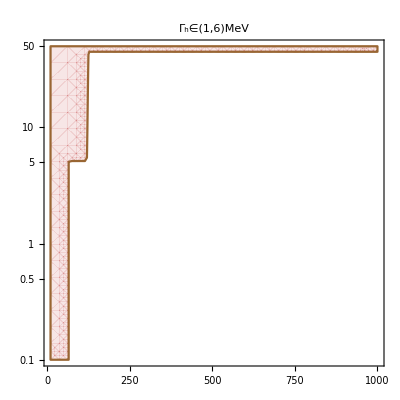

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {140.263,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

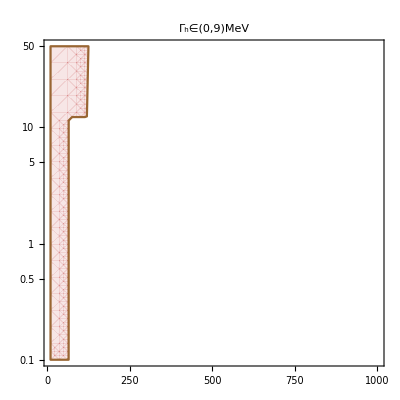

```mathematica
haa=Table[Max[results[[j,33]]],{j,1,leng}];

datahaa=Table[{mH[[j]],tb[[j]],haa[[j]]},{j,1,leng} ];


funchaa=Interpolation[datahaa,InterpolationOrder->1];

(*Exclusion Plots*)
clightbrwon=RGBColor[205/255,92/255,92/255](*165,42,42*)
(*Exclusion Plots*)
fcolA=Directive[clightbrwon,Opacity[0.15] ];lcolA=Brown;
figg=RegionPlot[funchaa[x,y]>6||funchaa[x,y]<1,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLabel->"Γ_h∈(1,6)MeV"]
figg=RegionPlot[funchaa[x,y]>9||funchaa[x,y]<0.08,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLabel->"Γ_h∈(0,9)MeV"]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, HVV

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

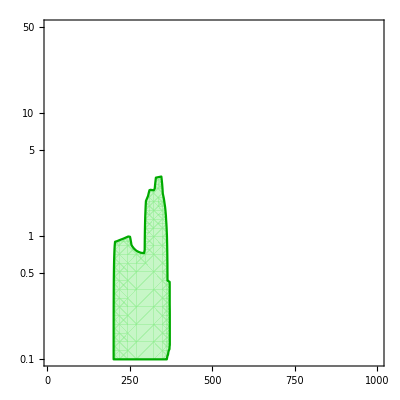

```mathematica
HVV=Table[Max[results[[j,3+2]],results[[j,5+2]],results[[j,6+2]]],{j,1,leng}];

dataHVV=Table[{mH[[j]],tb[[j]],HVV[[j]]},{j,1,leng} ];


funcHVV=Interpolation[dataHVV,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightgreen,Opacity[0.5] ];lcolA=Darker[Green];
figHVV=RegionPlot[funcHVV[x,y]>0.99,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

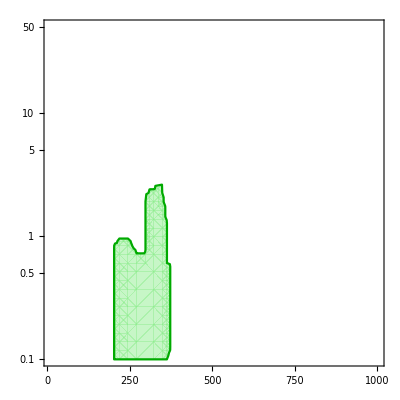
```mathematica
-Graphics-;
```

### Type-I, m_A=m_H, cos(β-α)=0.1, Htautau

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.0527,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

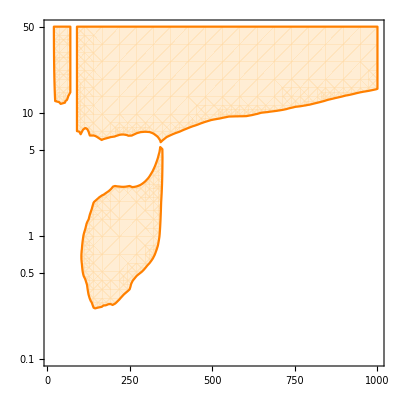

```mathematica
Htautau=Table[Max[results[[j,10+2]],results[[j,11+2]],results[[j,15+2]],results[[j,16+2]]],{j,1,leng}];
Htautau2=Table[results[[j,25+2]],{j,1,leng}];

dataHtautau=Table[{mH[[j]],tb[[j]],Htautau[[j]]},{j,1,leng} ];
dataHtautau2=Table[{mH[[j]],tb[[j]],Htautau2[[j]]},{j,1,leng} ];


funcHtautau=Interpolation[dataHtautau ,InterpolationOrder->1];
funcHtautau2=Interpolation[dataHtautau2 ,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightorange,Opacity[0.5] ];lcolA=Orange;
figHtautau=RegionPlot[funcHtautau[x,y]≥1&&x>90||funcHtautau2[x,y]≥1&&x<70&&x>20,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]

(*figHtautau2=RegionPlot[funcHtautau2[x,y]>0.9&&x<70&&x>20,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]*)
```

### Type-I, m_A=m_H, cos(β-α)=0.1, Hhh

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

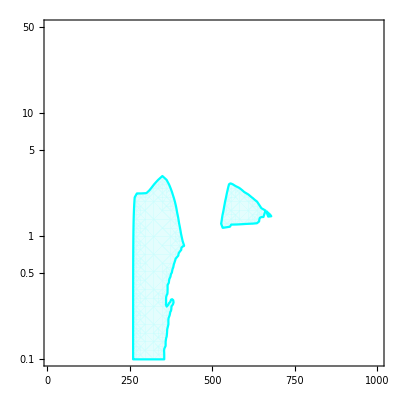

```mathematica
Hhh=Table[results[[j,4+2]],{j,1,leng}];

dataHhh=Table[{mH[[j]],tb[[j]],Hhh[[j]]},{j,1,leng} ];


funcHhh=Interpolation[dataHhh,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightcyan,Opacity[0.5] ];lcolA=Cyan;
figHhh=RegionPlot[funcHhh[x,y]>0.99,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

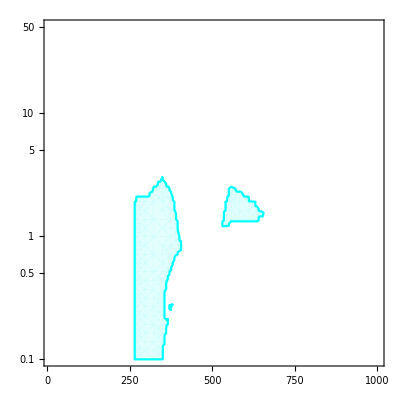
```mathematica
-Graphics-;
```

### Type-I, m_A=m_H, cos(β-α)=0.1, Hbb

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {296.579,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {817.632,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

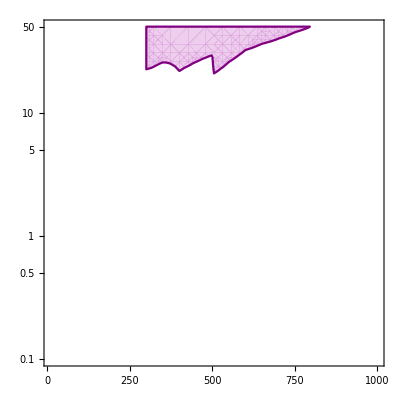

```mathematica
Hbb=Table[Max[results[[j,7+2]],results[[j,12+2]]],{j,1,leng}];

dataHbb=Table[{mH[[j]],tb[[j]],Hbb[[j]]},{j,1,leng} ];


funcHbb=Interpolation[dataHbb,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[clightpurple,Opacity[0.5] ];lcolA=Purple;
figHbb=RegionPlot[funcHbb[x,y]>0.99&&x≥300,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, Hmumu

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {140.263,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {505.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

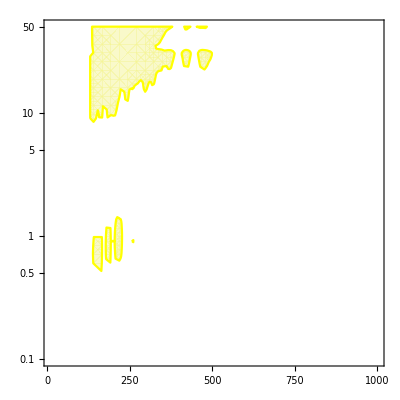

```mathematica
Hmumu=Table[Max[results[[j,8+2]],results[[j,9+2]],results[[j,13+2]],results[[j,14+2]]],{j,1,leng}];

dataHmumu=Table[{mH[[j]],tb[[j]],Hmumu[[j]]},{j,1,leng} ];


funcHmumu=Interpolation[dataHmumu,InterpolationOrder->2];

(*Exclusion Plots*)
fcolA=Directive[clightyellow,Opacity[0.5] ];lcolA=Yellow;
figHmumu=RegionPlot[funcHmumu[x,y]≥1&&x>130,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, Ayy

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

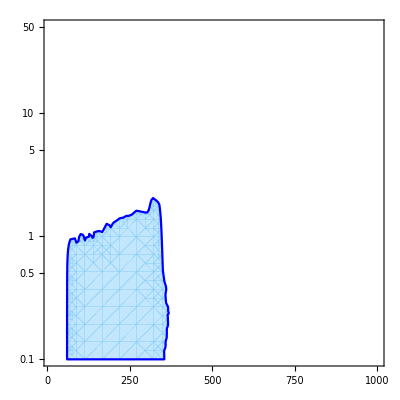

```mathematica
Ayy=Table[Max[results[[j,23]],results[[j,24]],results[[j,25]],results[[j,26]]],{j,1,leng}];
(*Ayy=Table[results[[j,23]]^2+results[[j,24]]^2+results[[j,25]]^2+results[[j,26]]^2,{j,1,leng}];*)

dataAyy=Table[{mH[[j]],tb[[j]],Ayy[[j]]},{j,1,leng} ];


funcAyy=Interpolation[dataAyy,InterpolationOrder->2];

(*Exclusion Plots*)
fcolA=Directive[clightskyblue,Opacity[0.5] ];lcolA=Blue;
figAyy=RegionPlot[funcAyy[x,y]>0.99,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

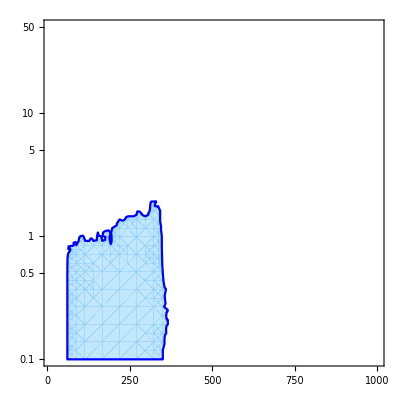
```mathematica
-Graphics-;
```

#### ana

/Users/weisu/Documents/research/project/114a/LHC_HZA/1new_code/My2HDMC0408/data_mh2tb/

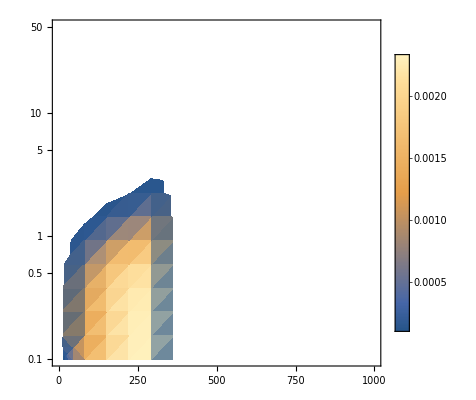

```mathematica
xmin=10;xmax=1000;ymin=Log10[0.1];ymax=Log10[50];

(*Import Stuff*)
PathDir=NotebookDirectory[]
results00=Import[PathDir<>"mh2tb_20.05_noexo.txt","table"];
leng00=Length[results00];
mH00=Table[results00[[j,3]],{j,1,leng00}];
tb00=Table[Log10[results00[[j,5]]],{j,1,leng00}];
brAyy00=Table[results00[[j,21]],{j,1,leng00}];
dataAyy00=Table[{mH00[[j]],tb00[[j]],brAyy00[[j]]},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic,PlotRange->{0.0001,1}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, Htt

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

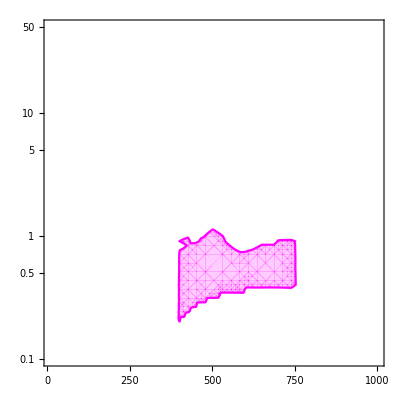

```mathematica
Htt=Table[Max[results[[j,21]],results[[j,22]]],{j,1,leng}];

dataHtt=Table[{mH[[j]],tb[[j]],Htt[[j]]},{j,1,leng} ];


funcHtt=Interpolation[dataHtt,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[Magenta,Opacity[0.2] ];lcolA=Magenta;
figHtt=RegionPlot[funcHtt[x,y]≥1,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, ttHtt

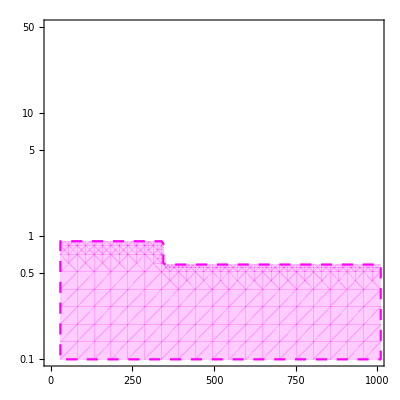

```mathematica
fun4t[x_]:=If[x≤ 345,Log10[1/1.1],Log10[1/1.7]];
fcolA=Directive[Magenta,Opacity[0.2] ];
d=8;
lcolA=Directive[AbsoluteDashing[{d,15-d}],Magenta];
fig4t=RegionPlot[y<=fun4t[x],{x,30,1010},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotRange->{{0,1000},{-1,1.7}}]
```

### Type-I, m_A=m_H, cos(β-α)=0.1, haa

```mathematica
haa=Table[Max[results[[j,28]],results[[j,29]],results[[j,30]]],{j,1,leng}];

datahaa=Table[{mH[[j]],tb[[j]],haa[[j]]},{j,1,leng} ];


funchaa=Interpolation[datahaa,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[Magenta,Opacity[0.2] ];lcolA=Magenta;
fighaa=RegionPlot[funchaa[x,y]≥1,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

-Graphics-

#### ana

/Users/weisu/Documents/research/project/114a/LHC_HZA/1new_code/My2HDMC0408/data_mh2tb/

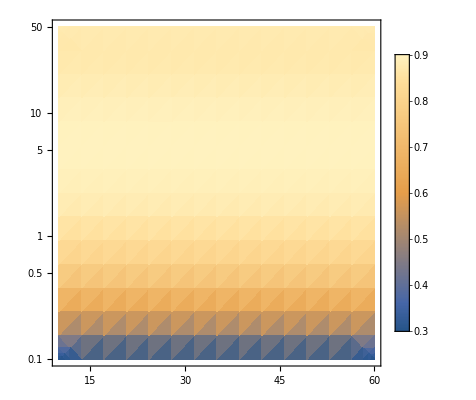

0.882186

```mathematica
xmin=10;xmax=1000;ymin=Log10[0.1];ymax=Log10[50];

(*Import Stuff*)
PathDir=NotebookDirectory[]
results00=Import[PathDir<>"mh2tb_20.05_noexo.txt","table"];
(*infile1>>mh>>mH>>mA>>cosba>>tb;5
infile1>>ggA8>>bbA8;2
infile1>>ggA13>>bbA13>>zA13>>wbfA13;4
infile1>>ggH13>>bbH13>>zH13>>wbfH13;4
infile1>>brAtautau>>brAmumu>>brAbb>>brAtt;4
infile1>>brAgg>>brAgaga>>brAzh>>brHtautau;4
infile1>>brHmumu>>brHbb>>brHtt>>brHZZ;4
infile1>>brHWW>>brHhh>>brHgg>>brHgaga;4
infile1>>brhbb>>brHAZ>>brAHZ;3
infile1>>gammatotH>>gammatotA;2
infile1>>ggh13>>bbh13>>WBFh13;3
infile1>>Zh13>>brhaa>>brhHH;3
infile1>>ggA8>>bbA8>>WBFA8>>ZA8;4
infile1>>ggH8>>bbH8>>WBFH8>>ZH8;4
*)
leng00=Length[results00];
mH00=Table[results00[[j,3]],{j,1,leng00}];
tb00=Table[Log10[results00[[j,5]]],{j,1,leng00}];
prAyy00=Table[results00[[j,40]]+results00[[j,39]]+results00[[j,38]]+results00[[j,37]],{j,1,leng00}];
dataAyy00=Table[{mH00[[j]],tb00[[j]],prAyy00[[j]]/50},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,60},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic(*PlotRange->{0.0001,1}*),Mesh->{Range[-1,1,0.4],Range[0.8,0.4]},MeshStyle->{Black,Dashed}]
funcAyy00[60,Log10[45]]
```

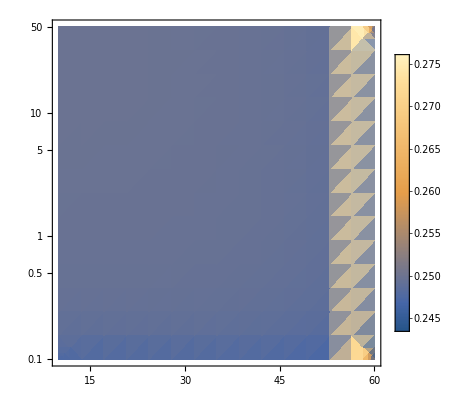

0.247395

```mathematica
(*haa*)
brAyy00=Table[results00[[j,41]],{j,1,leng00}];
dataAyy00=Table[{mH00[[j]],tb00[[j]],brAyy00[[j]]},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,60},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic,PlotRange->{0.0001,1}]
funcAyy00[60,Log10[45]]
```

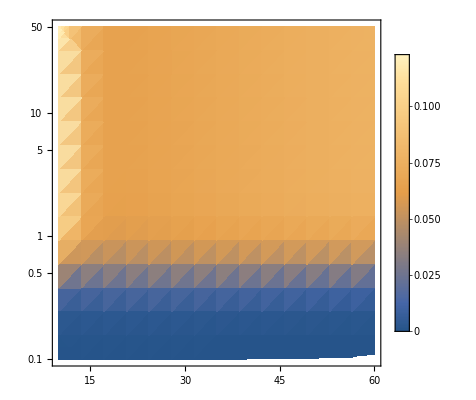

0.0769925

```mathematica
(*atautau*)
brAtautau00=Table[results00[[j,16]],{j,1,leng00}];
dataAyy00=Table[{mH00[[j]],tb00[[j]],brAtautau00[[j]]},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,60},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic,PlotRange->{0.0001,1}]
funcAyy00[60,Log10[45]]
```

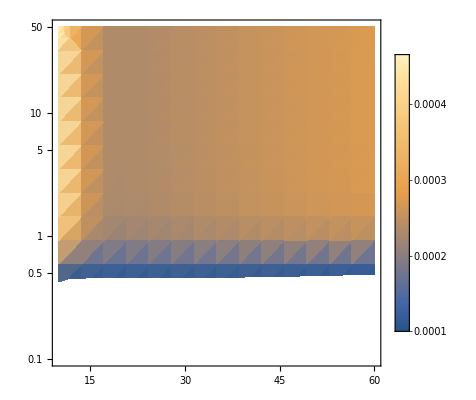

0.000272722

```mathematica
(*amumu*)
brAyy00=Table[results00[[j,17]],{j,1,leng00}];
dataAyy00=Table[{mH00[[j]],tb00[[j]],brAyy00[[j]]},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,60},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic,PlotRange->{0.0001,1}]
funcAyy00[60,Log10[45]]
```

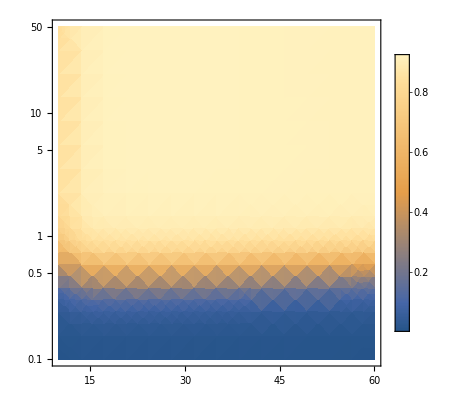

0.918829

```mathematica
(*abb*)
brAbb00=Table[results00[[j,18]],{j,1,leng00}];
dataAyy00=Table[{mH00[[j]],tb00[[j]],brAbb00[[j]]},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,60},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic,PlotRange->{0.0001,1}]
funcAyy00[60,Log10[45]]
```

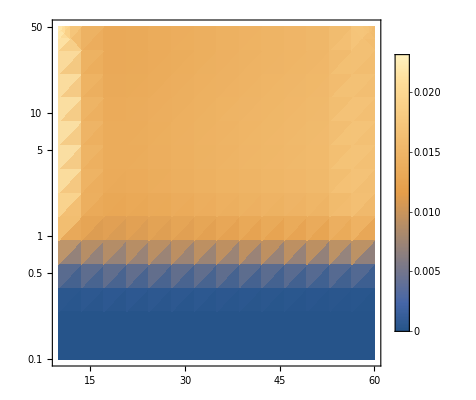

0.0154395

```mathematica
(*brAyy00=Table[results00[[j,40]]+results00[[j,39]]+results00[[j,38]]+results00[[j,37]],{j,1,leng00}];*)
dataAyy00=Table[{mH00[[j]],tb00[[j]],prAyy00[[j]]*brAyy00[[j]]*brAbb00[[j]]*brAtautau00[[j]]/50},{j,1,leng00} ];
funcAyy00=Interpolation[dataAyy00,InterpolationOrder->2];
DensityPlot[funcAyy00[x,y],{x,xmin,60},{y,ymin,ymax},MaxRecursion->3,FrameTicks->{{ticksyaxis,None},{Automatic,None}},PlotLegends->Automatic(*PlotRange->{0.0001,1}*)]
funcAyy00[60,Log10[45]]
```

```mathematica
funcAyy00[50,Log10[40]]
```

0.0149734

### Type-I, m_A=m_H, cos(β-α)=0.1, Γ width

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

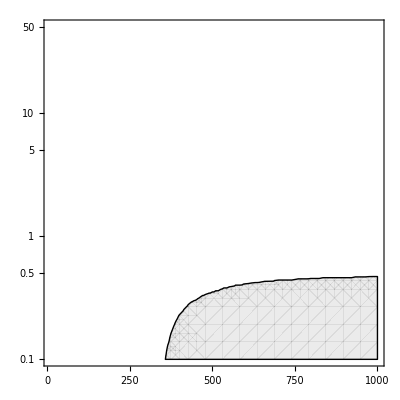

```mathematica
width=Table[Max[results[[j,32]]],{j,1,leng}];

datawidth=Table[{mH[[j]],tb[[j]],width[[j]]},{j,1,leng} ];


funcwidth=Interpolation[datawidth,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[GrayLevel[0.61,0.2]];lcolA=Directive[Black,Thin];
figwidth=RegionPlot[funcwidth[x,y]≥0.2,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

```mathematica
width=Table[Max[results[[j,31]],results[[j,32]]],{j,1,leng}];

datawidth=Table[{mH[[j]],tb[[j]],width[[j]]},{j,1,leng} ];


funcwidth2=Interpolation[datawidth,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[GrayLevel[0.61,0.2]];lcolA=Directive[Black,Thin];
figwidth=RegionPlot[funcwidth[x,y]≥0.2,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {0.0526842,-0.999858} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1000.,1.69897} lies outside the range of data in the interpolating function. Extrapolation will be used.

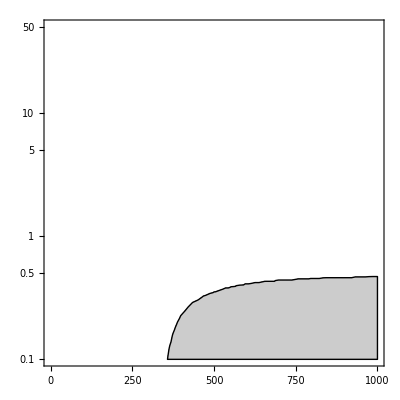

```mathematica
width=Table[Max[results[[j,31]],results[[j,32]]],{j,1,leng}];

datawidth=Table[{mH[[j]],tb[[j]],width[[j]]},{j,1,leng} ];


funcwidth2=Interpolation[datawidth,InterpolationOrder->1];

(*Exclusion Plots*)
fcolA=Directive[GrayLevel[0.8]];lcolA=Directive[Black,Thin];
figwidth2=RegionPlot[funcwidth[x,y]≥0.2,{x,xmin,xmax},{y,ymin,ymax},MaxRecursion->3,BoundaryStyle->lcolA,PlotStyle-> fcolA,FrameTicks->{{ticksyaxis,None},{Automatic,None}}]
```

### Frame

0

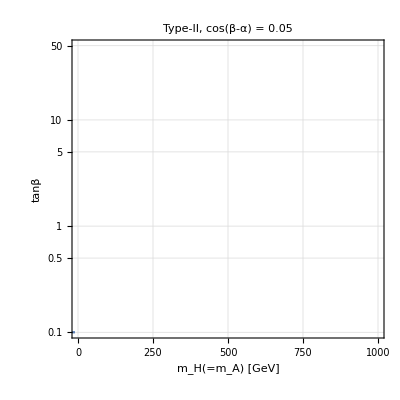

```mathematica
(*Create a nice looking Frame*)
SetOptions[ListPlot,BaseStyle->{FontSize->15}];
ticksyaxis = { 
 {Log10[0.1],"0.1"(*Superscript[10,-1]*)},{Log10[0.2],""},{Log10[0.3],""},{Log10[0.4],""},
{Log10[0.5],"0.5"},{Log10[0.6],""},{Log10[0.7],""},{Log10[0.8],""},{Log10[0.9],""},
 {Log10[1],1},{Log10[2],""},{Log10[3],""},{Log10[4],""},
{Log10[5],"5"},{Log10[6],""},{Log10[7],""},{Log10[8],""},{Log10[9],""},
 {Log10[10],10},{Log10[20],""},{Log10[30],""},{Log10[40],""},
{Log10[50],"50"},{Log10[60],""},{Log10[70],""},{Log10[80],""},{Log10[90],""},
 {Log10[100],100}};
xmin=0；
xmax=1000;
yellow2=RGBColor[241/255,240/255,0];
MyFrame=ListPlot[{{-10,-1},{-20,-1}},
PlotRange->{{xmin,xmax},{ymin,ymax}},
Frame->True, Axes->False,AspectRatio->1,FrameStyle->Directive[Black,Thick],
Joined->True,Filling->None,
GridLines->Automatic,
FrameTicks->{{ticksyaxis,None},{Automatic,None}},
FrameLabel->{Style["m_H(=m_A) [GeV]",Black,16],Style["tanβ",Black,16]},
PlotLabel->Style["Type-II, cos(β-α) = 0.05",Black,14],
Epilog->{
(*Inset[Style["m_H = 200 [GeV]",Red,15],{600,Log10[15.7]}],
Inset[Style["m_H = 250 [GeV]",Darker[Green],15],{600,Log10[10]}],
Inset[Style["m_H = 150 [GeV]",Blue,15],{600,Log10[25]}]*)
(*{Red,Rectangle[{150,1.4},{180,1.5}]},
Text[Style["A→Zh(h→bb^-)" ,FontSize->13.5,Red],{190,1.45},{-1,0},{1,0}],

{Purple,Rectangle[{150,1.2},{180,1.3}]},
Text[Style["A/H → bb^-",FontSize->13.5,Purple],{190,1.25},{-1,0},{1,0}],

{Cyan,Rectangle[{420+35,1.4},{450+35,1.5}]},
Text[Style["H → hh",FontSize->13.5,Cyan],{460+35,1.45},{-1,0},{1,0}],

{yellow2,Rectangle[{420+35,1.2},{450+35,1.3}]},
Text[Style["A/H → μμ",FontSize->13.5,yellow2],{460+35,1.25},{-1,0},{1,0}],

{Darker[Green],Rectangle[{700,1.4},{730,1.5}]},
Text[Style["H → VV",FontSize->13.5,Darker[Green]],{740,1.45},{-1,0},{1,0}],

{Orange,Rectangle[{700,1.2},{730,1.3}]},
Text[Style["A/H → ττ",FontSize->13.5,Orange],{740,1.25},{-1,0},{1,0}],*)

},
ImageSize->400]
```

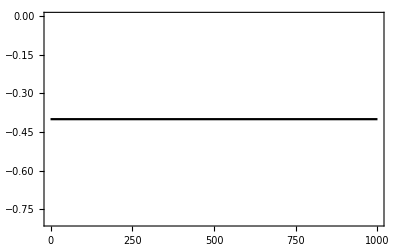

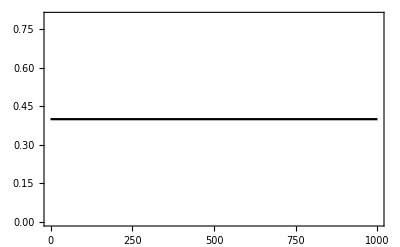

```mathematica
a=ListPlot[{{0,-0.4},{1000,-0.4}},PlotStyle->Black,Joined->True,Frame->True]
b=ListPlot[{{0,0.4},{1000,0.4}},PlotStyle->Black,Joined->True,Frame->True]
```

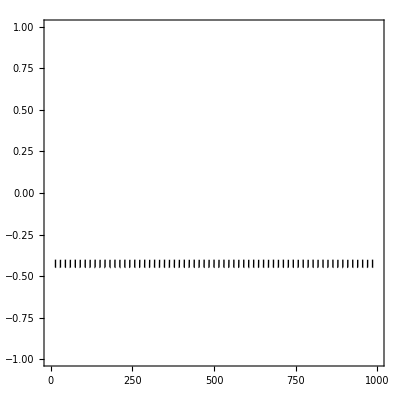

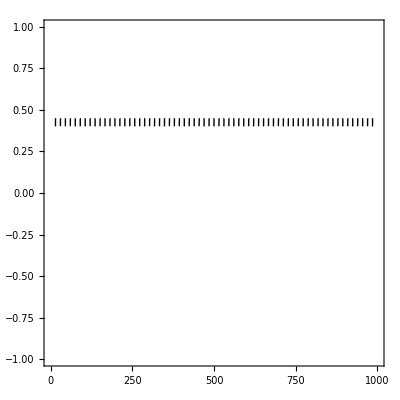

```mathematica
cepcmesh1=ContourPlot[y,{x,0,1000},{y,-1,1},Contours->{-0.36},ContourStyle->Directive[Blue,Thick],ContourShading->{None,None},PlotRange->{{0,1000},{-1,1}},PlotPoints->100,Mesh->{65},MeshFunctions->{#1-#2&},MeshStyle->Directive[Thin,Black],RegionFunction->(-0.45≤#2≤-0.4&)]
cepcmesh2=ContourPlot[y,{x,0,1000},{y,-1,1},Contours->{-0.36},ContourStyle->Directive[Blue,Thick],ContourShading->{None,None},PlotRange->{{0,1000},{-1,1}},PlotPoints->100,Mesh->{65},MeshFunctions->{#1-#2&},MeshStyle->Directive[Thin,Black],RegionFunction->(0.4≤#2≤0.45&)]
```

### Results

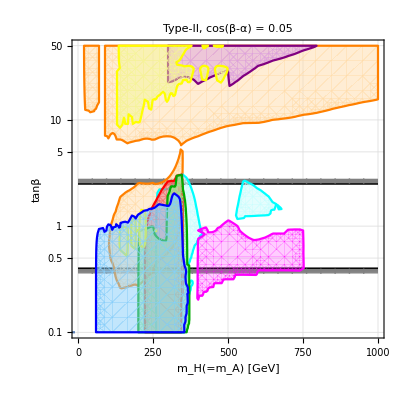

```mathematica
(*Combine Everything*)
combined=Show[MyFrame,a,b,cepcmesh1,cepcmesh2,figHtautau,figHhh,figAzhbb,figHVV,figHbb,figHmumu,figAyy,figHtt]
Export[PathDir<>"mHtb2005_noexo.pdf",%];
```

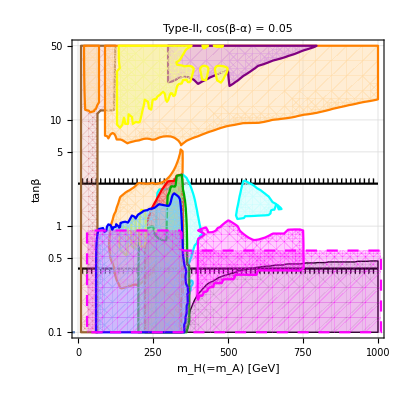

```mathematica
combined=Show[MyFrame,figwidth,a,b,cepcmesh1,cepcmesh2,figg,figHtautau,figHhh,figAzhbb,figHVV,figHbb,figHmumu,figAyy,fig4t,figHtt]
Export[PathDir<>"mHtb2005_noexobackup.pdf",%,ImageResolution->400];
```

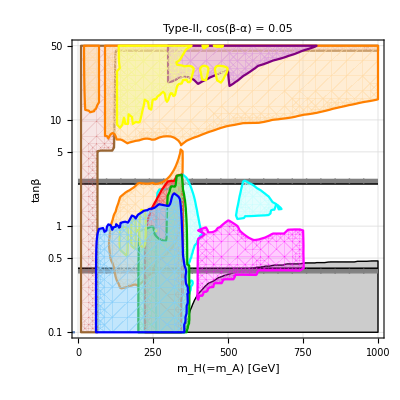

```mathematica
combined=Show[MyFrame,figwidth2,a,b,cepcmesh1,cepcmesh2,figg,figHtautau,figHhh,figAzhbb,figHVV,figHbb,figHmumu,figAyy,figHtt]
Export[PathDir<>"mHtb2005_noexobackup2.pdf",%,ImageResolution->400];
```

```mathematica
NotebookSave[];
```